```mathematica
(*Define constants of the problem*)
kBT=1.380649*10^(-23) * 200 * 10^-9;
a0=5.29*10^(-11);
hPlanck=6.62607015*10^(-34);
hbar=hPlanck/(2*Pi);
muNa40K=14.594251717637002*1.660538782*10^(-27);
ai=-1700 * a0;
af=640 * a0;
(*energies in units of kBT*)
Ei=hbar^2/(2*muNa40K*ai^2) / kBT;
Ef=hbar^2/(2*muNa40K*af^2) / kBT;
```

```mathematica
(*Lineshape from first-order calculation*)
```

```mathematica
pCOM=pNa+pK;
mu=mNa*mK/(mNa+mK);
pRel=(pNa/mNa-pK/mK)*mu;
mTot=mNa+mK;
```

```mathematica
pCOM^2/(2(mNa+mK))+pRel^2/(2*mu)//FullSimplify
```

1/2 (pK^2/mK+pNa^2/mNa)

```mathematica
T[w_,a_]:=1/(1/a - Sqrt[-w]);
```

```mathematica
f[x_]:=NIntegrate[P^2 *Exp[-P^2]*T[x-P^2,1],{P,0,100}];
```

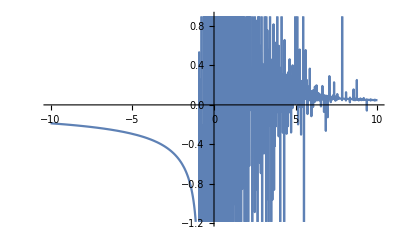

```mathematica
Plot[Re[f[x]],{x,-10,10}]
```